```mathematica
TI - GibbsBogoliubov -mean value theorem;
```

```mathematica
Import ab intio data;
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Thermodynamic_Integration_Analysis"];
(*The file T_dudl_meam_4801 contains TILD data - temp and dUdL, for 11 lambda values 0.0 to 1.0 in 0.1 steps. The data is for ZrC 4.801Angstrom*)
filesEinsteinPot={"T_dudl_meam_4685","T_dudl_meam_4801"};
TdUdL4801=ReadList[filesEinsteinPot[[2]],{Number, Number}];
TdUdL4685=ReadList[filesEinsteinPot[[1]],{Number, Number}];
temps={300,760,1900,2500,3200,3805};
lambda=Table[i/10,{i,0,10}]//N;
```

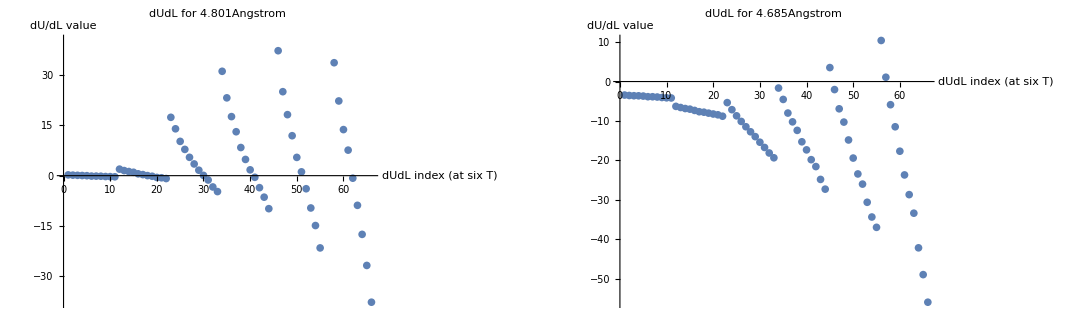

```mathematica
Plot dU/dL data;
(*dUdL given at 6 temperatures - for each of which there are 11 dUdL points - 0.0, 0.1 0.2 .... 1.0 *)
dudlplot1=ListPlot[Transpose[TdUdL4801][[2]],PlotLabel->"dUdL for 4.801Angstrom",AxesLabel->{"dUdL index \n(at six T)","dU/dL value"},ImageSize->500];
dudlplot2=ListPlot[Transpose[TdUdL4685][[2]],PlotLabel->"dUdL for 4.685Angstrom",AxesLabel->{"dUdL index \n(at six T)","dU/dL value"},ImageSize->500];
GraphicsGrid[{{dudlplot1,dudlplot2}}]
```

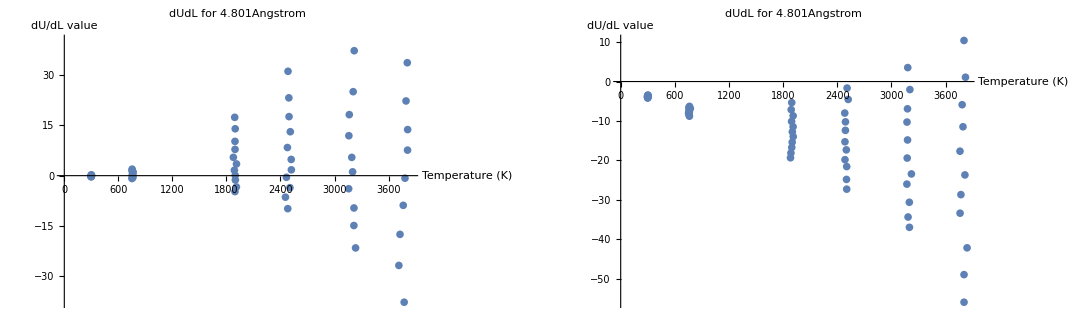

```mathematica
Plot dU/dL data at temperatures;dudlTplotinfo1={PlotLabel->"dUdL for 4.801Angstrom",AxesLabel->{"Temperature (K)","dU/dL value"},ImageSize->500};
dudlT1plot=ListPlot[TdUdL4801,dudlTplotinfo1];
dudlTplotinfo2={PlotLabel->"dUdL for 4.801Angstrom",AxesLabel->{"Temperature (K)","dU/dL value"},ImageSize->500};
dudlT2plot=ListPlot[TdUdL4685,dudlTplotinfo2];
GraphicsGrid[{{dudlT1plot,dudlT2plot}}]
```

```mathematica
Fit polynomial;
(*make the dUdL at function of lambda*)
dUdL4801=Partition[Transpose[TdUdL4801][[2]],11];
dudlLambda4801=Table[Transpose@{lambda,dUdL4801[[i]]},{i,1,6}];
dUdL4685=Partition[Transpose[TdUdL4685][[2]],11];
dudlLambda4685=Table[Transpose@{lambda,dUdL4685[[i]]},{i,1,6}];
(*Fit polynomal function of dudl (in lambda) *)
dudlLambdaFits4801=Table[Fit[dudlLambda4801[[i]],{1,x,x^2,x^3,x^4},x],{i,1,6}];
dudlLambdaFits4685=Table[Fit[dudlLambda4685[[i]],{1,x,x^2,x^3,x^4},x],{i,1,6}];
```

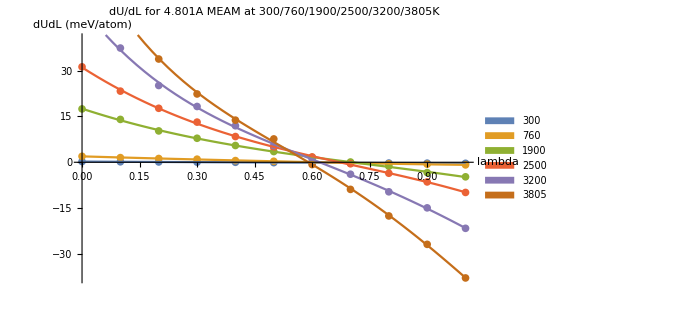

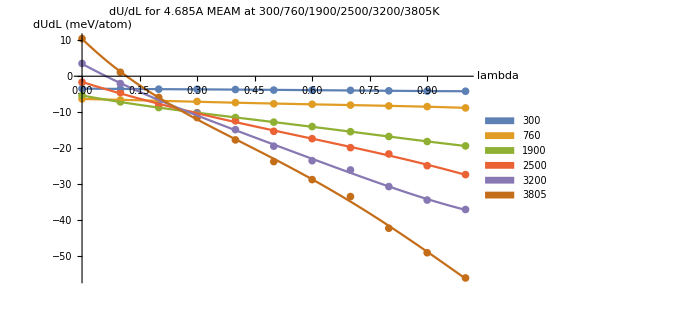

```mathematica
Plot polynomial and data;
(*Plot the dUdL data as a function of lambda, along witht fits, for both 4.685 and 4.801Angstrom*)
(*4801Angstrom*)
dudlLambdaplotinfo4801={PlotLabel->"dU/dL for 4.801A MEAM at 300/760/1900/2500/3200/3805K",ImageSize->500,AxesLabel->{"lambda","dUdL \n(meV/atom)"}};
dudlplot4801=Plot[Evaluate@dudlLambdaFits4801,{x,0,1},PlotLegends->SwatchLegend[temps]];
dudldataplot4801=ListPlot[dudlLambda4801,dudlLambdaplotinfo4801];
plot4801=Show[dudldataplot4801,dudlplot4801]
(*4685Angstrom*)
dudlLambdaplotinfo4685={PlotLabel->"dU/dL for 4.685A MEAM at 300/760/1900/2500/3200/3805K",ImageSize->500,AxesLabel->{"lambda","dUdL \n(meV/atom)"}};
dudlplot4685=Plot[Evaluate@dudlLambdaFits4685,{x,0,1},PlotLegends->SwatchLegend[temps]];
dudldataplot4685=ListPlot[dudlLambda4685,dudlLambdaplotinfo4685];
plot4685=Show[dudldataplot4685,dudlplot4685]
```

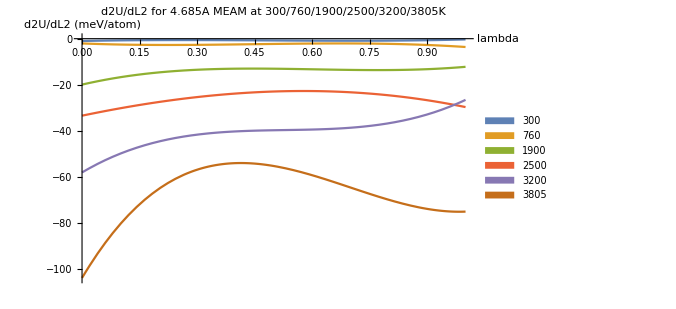

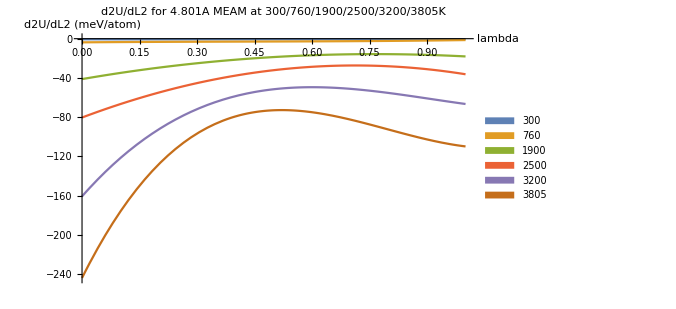

```mathematica
Plot second derivative in lambda;
(*Plot gradients 4.685angstrom*)
DdudlLambda4685=D[dudlLambdaFits4685,x];
DdudlLambdaplotinfo4685={PlotLabel->"d2U/dL2 for 4.685A MEAM at 300/760/1900/2500/3200/3805K",ImageSize->500,AxesLabel->{"lambda","d2U/dL2 \n(meV/atom)"}};
Plot[Evaluate@Table[DdudlLambda4685[[j]],{j,1,6}],{x,0,1},Evaluate@DdudlLambdaplotinfo4685,PlotLegends->SwatchLegend[temps]]
(*Plot gradients 4.685angstrom*)
DdudlLambda4801=D[dudlLambdaFits4801,x];
DdudlLambdaplotinfo4801={PlotLabel->"d2U/dL2 for 4.801A MEAM at 300/760/1900/2500/3200/3805K",ImageSize->500,AxesLabel->{"lambda","d2U/dL2 \n(meV/atom)"}};
Plot[Evaluate@Table[DdudlLambda4801[[j]],{j,1,6}],{x,0,1},Evaluate@DdudlLambdaplotinfo4801,PlotLegends->SwatchLegend[temps]]
```

```mathematica
Plot second derivative with limits as linear extrapolations of the gradients at the lambda extrema;
```

```mathematica
limit0=(dudlLambdaFits4801/.x->0)+(DdudlLambda4801/.x->0)x;
limit1=(dudlLambdaFits4801/.x->1)-(DdudlLambda4801/.x->1)+(DdudlLambda4801/.x->1)x;
dataplot=Table[{limit0[[i]],limit1[[i]],dudlLambdaFits4801[[i]]},{i,1,6}];

limit04685=(dudlLambdaFits4685/.x->0)+(DdudlLambda4685/.x->0)x;
limit14685=(dudlLambdaFits4685/.x->1)-(DdudlLambda4685/.x->1)+(DdudlLambda4685/.x->1)x;
dataplot4685=Table[{limit04685[[i]],limit14685[[i]],dudlLambdaFits4685[[i]]},{i,1,6}];

swatchlabels={"l=0 limit","l=1 limit", "dU/dL"};
ps1={PlotLabel->temps[[i]]"K",AxesLabel->{"","dU/dL"},PlotLegends->Placed[SwatchLegend[swatchlabels],{0.5,0.9}],ImageSize->800}
```

Part::pkspec1: The expression i cannot be used as a part specification.

{PlotLabel→K {300,760,1900,2500,3200,3805}⟦i⟧,AxesLabel→{,dU/dL},PlotLegends→Placed[SwatchLegend[{l=0 limit,l=1 limit,dU/dL}],{0.5,0.9}],ImageSize→800}

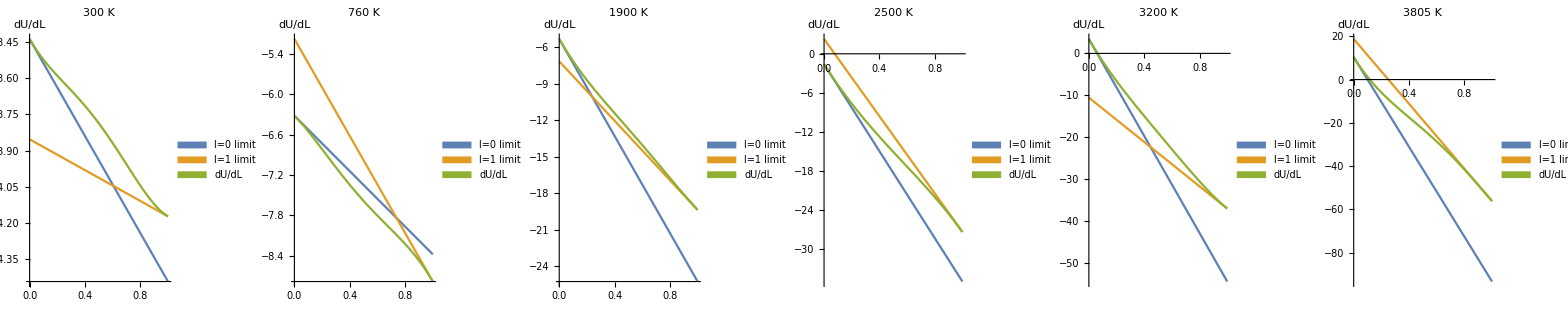
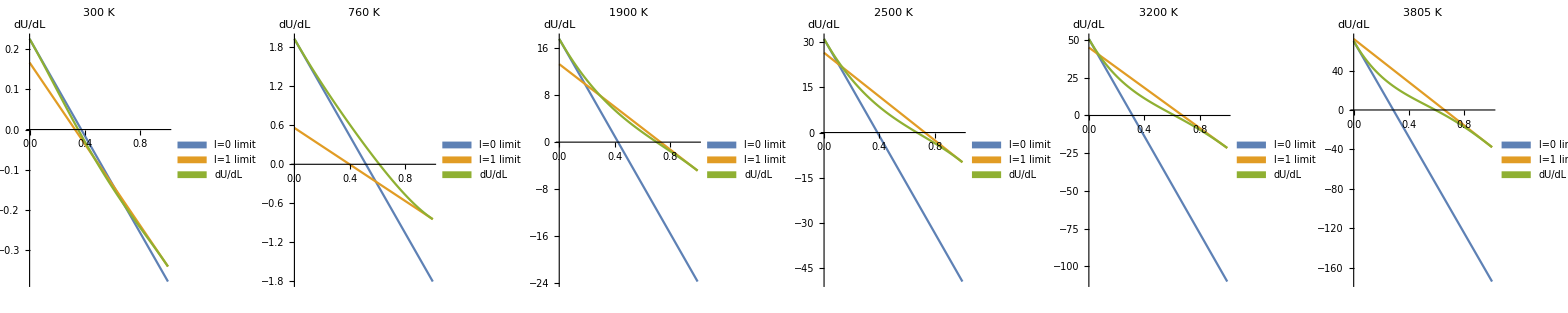

```mathematica
GraphicsGrid[{Table[Plot[Evaluate@dataplot[[i]],{x,0,1},Evaluate@(ps1/.y->temps[[1]])],{i,1,6}]},ImageSize->2500]

GraphicsGrid[{Table[Plot[Evaluate@dataplot4685[[i]],{x,0,1},Evaluate@(ps1/.y->temps[[1]])],{i,1,6}]},ImageSize->2500]
```

{PlotLabel→T=300K 4.801Ang,AxesLabel→{,dU/dL},PlotLegends→Placed[SwatchLegend[{l=0 limit,l=1 limit,dU/dL}],{0.5,0.9}],ImageSize→800}

300

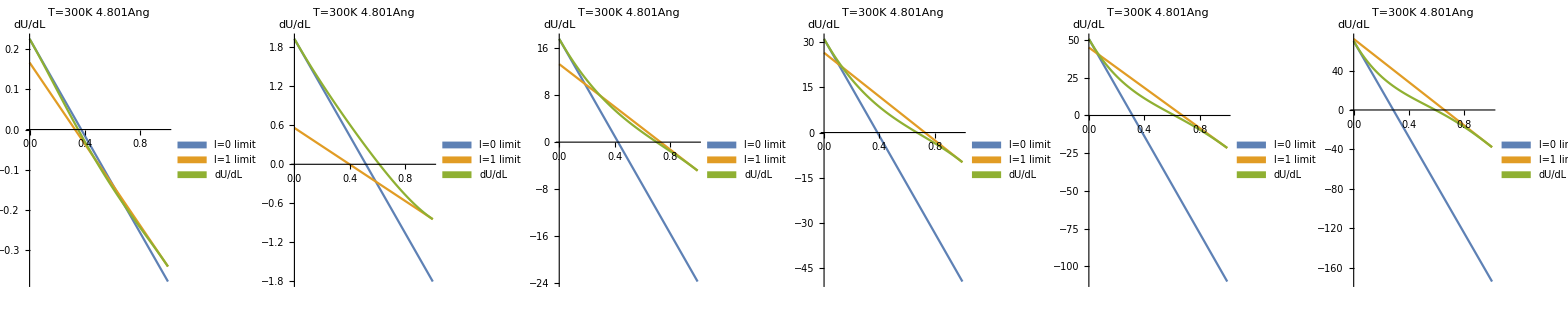

```mathematica
GraphicsGrid[{{Plot[Evaluate@dataplot[[1]],{x,0,1},Evaluate@ps1],Plot[Evaluate@dataplot[[2]],{x,0,1},Evaluate@ps1],Plot[Evaluate@dataplot[[3]],{x,0,1},Evaluate@ps1],Plot[Evaluate@dataplot[[4]],{x,0,1},Evaluate@ps1],Plot[Evaluate@dataplot[[5]],{x,0,1},Evaluate@ps1],Plot[Evaluate@dataplot[[6]],{x,0,1},Evaluate@ps1]}},ImageSize->2500]
```

```mathematica
Fit dUdL data to analytic function eg polynomial;
dudl300=Fit[dudl[[1]],{1,x,x^2,x^3,x^4},x];
dudl760=Fit[dudl[[2]],{1,x,x^2,x^3,x^4},x];
dudl1900=Fit[dudl[[3]],{1,x,x^2,x^3,x^4},x];
dudl2500=Fit[dudl[[4]],{1,x,x^2,x^3,x^4},x];
dudl3200=Fit[dudl[[5]],{1,x,x^2,x^3,x^4},x];
dudl3805=Fit[dudl[[6]],{1,x,x^2,x^3,x^4},x];
dudlall={dudl300,dudl760,dudl1900,dudl2500,dudl3200,dudl3805};
plotinfo={PlotLabel->"dU/dL for 4.801A MEAM at 300/760/1900/2500/3200/3805K"};
dudldataplot=ListPlot[dudl,plotinfo];
dudlfitplot=Plot[dudlall,{x,1,11}];
Show[dudldataplot,dudlfitplot,ImageSize->500]
```

Part::partd: Part specification dudl⟦1⟧ is longer than depth of object.

Fit::fitd: First argument dudl⟦1⟧ in Fit is not a list or a rectangular array.

Part::partd: Part specification dudl⟦2⟧ is longer than depth of object.

Fit::fitd: First argument dudl⟦2⟧ in Fit is not a list or a rectangular array.

Part::partd: Part specification dudl⟦3⟧ is longer than depth of object.

Fit::fitd: First argument dudl⟦3⟧ in Fit is not a list or a rectangular array.

Part::partd: Part specification dudl⟦4⟧ is longer than depth of object.

Fit::fitd: First argument dudl⟦4⟧ in Fit is not a list or a rectangular array.

Part::partd: Part specification dudl⟦5⟧ is longer than depth of object.

Fit::fitd: First argument dudl⟦5⟧ in Fit is not a list or a rectangular array.

Part::partd: Part specification dudl⟦6⟧ is longer than depth of object.

Fit::fitd: First argument dudl⟦6⟧ in Fit is not a list or a rectangular array.

ListPlot::lpn: dudl is not a list of numbers or pairs of numbers.

General::ivar: 1.0002 is not a valid variable.

General::ivar: 1.20429 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[dudl,{PlotLabel→dU/dL for 4.801A MEAM at 300/760/1900/2500/3200/3805K}],,ImageSize→500].

Show[ListPlot[dudl,{PlotLabel→dU/dL for 4.801A MEAM at 300/760/1900/2500/3200/3805K}],-Graphics-,ImageSize→500]

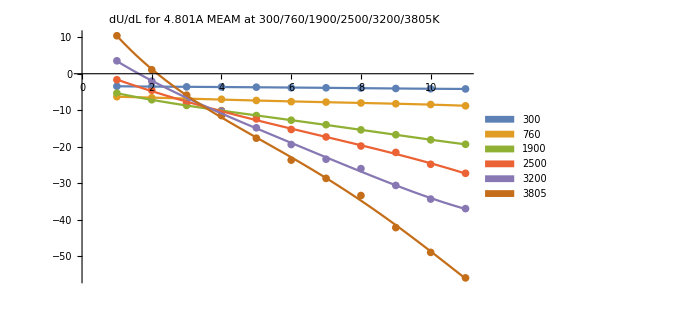

```mathematica
Partition[Transpose[TdUdL4685][[2]],10];
dudl4685=Partition[Transpose[TdUdL4685][[2]],11];
dudlall4685=Table[Fit[dudl4685[[i]],{1,x,x^2,x^3,x^4},x],{i,1,6}];
plotinfo4685={PlotLabel->"dU/dL for 4.801A MEAM at 300/760/1900/2500/3200/3805K"};
dudldataplot4685=ListPlot[dudl4685,plotinfo4685];
dudlfitplot4685=Plot[Evaluate@dudlall4685,{x,1,11},PlotLegends->SwatchLegend[temps]];
Show[dudldataplot4685,dudlfitplot4685,ImageSize->500];
```

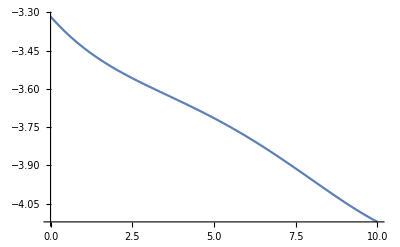

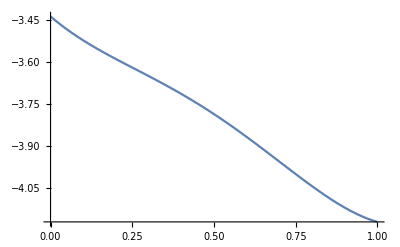

```mathematica
ftest[x_]:=-3.316060606060599-0.14640442890443303 x+0.028377039627040742 x^2-0.0038403263403264626 x^3+0.00016608391608392037 x^4
ftests[x_]:=ftest[10x+1]
Plot[ftest[x],{x,0,10}]
Plot[ftests[x],{x,0,1}]
```

{PlotLabel→dU/dL for 4.801A MEAM at 300/760/1900/2500/3200/3805K}

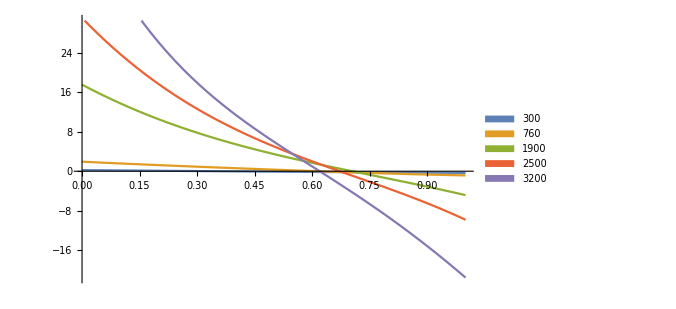

```mathematica
f300[x_]:=0.2818181818181814-0.05210761460761432 x-0.005224358974359101 x^2+0.0007905982905983082 x^3-0.00003205128205128275 x^4;
f760[x_]:=2.3206060606060563-0.41161033411032955 x+0.022164918414916947 x^2-0.002177544677544509 x^3+0.00010780885780885182 x^4;
f1900[x_]:=22.003030303030258-4.841093628593593 x+0.38293997668996543 x^2-0.015328282828281614 x^3+0.000032051282051242085 x^4;
f2500[x_]:=39.835454545454425-9.613092463092364 x+0.8356351981351678 x^2-0.03287490287489946 x^3-0.00008741258741270888 x^4;
f3200[x_]:=69.21727272727242-21.08800893550862 x+2.8012499999999 x^2-0.2041705516705405 x^3+0.005055361305360893 x^4;
f3805[x_]:=98.56575757575705-33.413321678321125 x+5.115011655011492 x^2-0.42052447552445726 x^3+0.011748251748251061 x^4;

f300s[x_]:=f300[10x+1]
f760s[x_]:=f760[10x+1]
f1900s[x_]:=f1900[10x+1]
f2500s[x_]:=f2500[10x+1]
f3200s[x_]:=f3200[10x+1]
f3805s[x_]:=f3805[10x+1]
fdudlall={f300s[x],f760s[x],f1900s[x],f2500s[x],f3200s[x],f3805s[x]};
plotinfo={PlotLabel->"dU/dL for 4.801A MEAM at 300/760/1900/2500/3200/3805K"}
dudlsplot=Plot[Evaluate@Table[fdudlall[[j]],{j,1,5}],{x,0,1},ImageSize->500,PlotLegends->SwatchLegend[temps]]
```

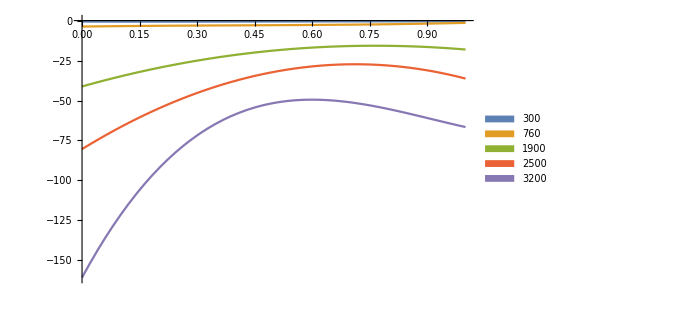

```mathematica
dduddl=D[fdudlall,x];
plotinfo1={PlotLabel->"d2U/dL2 for 4.801A MEAM at 300/760/1900/2500/3200/3805K"};
Plot[Evaluate@Table[dduddl[[j]],{j,1,5}],{x,0,1},ImageSize->500,PlotLegends->SwatchLegend[temps]]
```

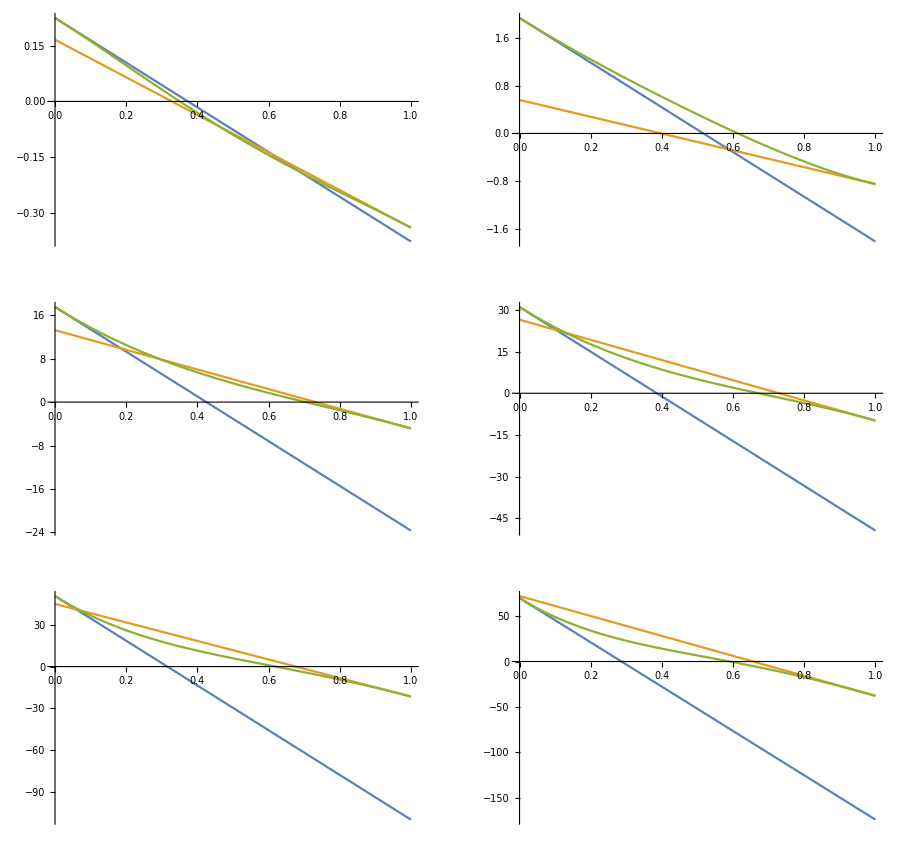

```mathematica
limit0=(fdudlall/.x->0)+(dduddl/.x->0)x;
limit1=(fdudlall/.x->1)-(dduddl/.x->1)+(dduddl/.x->1)x;
dataplot=Table[{limit0[[i]],limit1[[i]],fdudlall[[i]]},{i,1,6}];
GraphicsGrid[{Table[Plot[Evaluate@dataplot[[i]],{x,0,1}],{i,1,2}],Table[Plot[Evaluate@dataplot[[i]],{x,0,1}],{i,3,4}],Table[Plot[Evaluate@dataplot[[i]],{x,0,1}],{i,5,6}]},ImageSize->900]
```

Integrated dU/dL values:

{-0.076319,0.38386,4.42656,6.88962,8.43487,8.78051}

Finite difference

{-0.0576224,0.542028,6.34182,10.596,14.5982,16.0412}

Mean value theorem

{-0.0606037,0.463601,4.44004,6.69186,8.62813,10.3072}

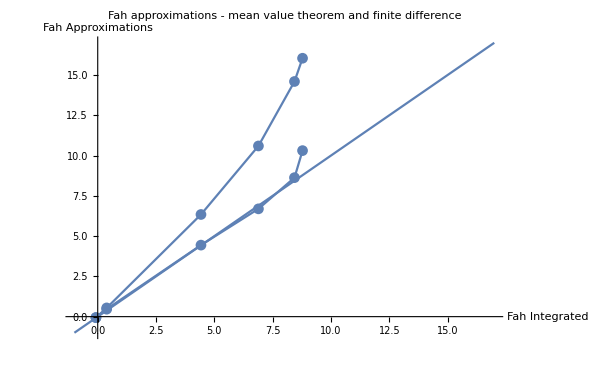

```mathematica
(*Test methods to get Fah*)
"Integrated dU/dL values:"
intVals=Integrate[fdudlall,{x,0,1}]
"Finite difference"
diffhalfVals=0.5((fdudlall/.x->1)+(fdudlall/.x->0))
"Mean value theorem"
halfVals=fdudlall/.x->0.45
(*Plotstuff*)
halfValsplot=ListPlot[Transpose@{intVals,halfVals}];
halfValsplotj=ListPlot[Transpose@{intVals,halfVals},Joined->True];
diffhalfValsplot=ListPlot[Transpose@{intVals,diffhalfVals}];
diffhalfValsplotj=ListPlot[Transpose@{intVals,diffhalfVals},Joined->True];
plotstuff={AxesLabel->{"Fah \n Integrated","Fah \n Approximations"},ImageSize->600,PlotLabel->"Fah approximations - mean value theorem and finite difference"};
(*Show normal integrated Fah for 4.801Ang  MEAM 6 temps*)
Show[ListPlot[intVals,AxesLabel->{"Index(T)","Fah"},PlotLabel->"Fah integrated for MEAM 4.801Ang\n T=300/760/1900/2500/3200/3805K",ImageSize->400],ListPlot[intVals,Joined->True]];
(*Show approximations to integrated Fah for 4.801Ang  MEAM 6 temps*)
Show[Plot[x,{x,-1,17},Evaluate@plotstuff],halfValsplotj,diffhalfValsplotj,halfValsplot,diffhalfValsplot]
```